Типовой расчет. Вариант 6

Задание 3

многочлен 1ого порядка:

Сумма квадратов отклонения в узлах для многочлена 1ой степени: 0.384863

многочлен 2ого порядка:

Сумма квадратов отклонения в узлах для многочлена 1ой степени: 0.106163

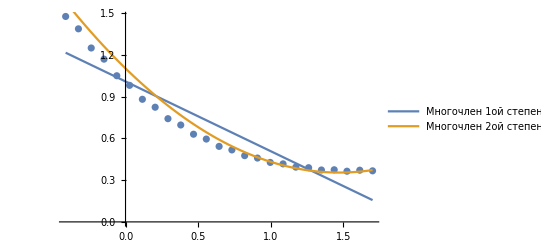

```mathematica
"Типовой расчет. Вариант 6"
"Задание 3"
(*Табличные данные*)
data= {{-0.412,1.47756},{-0.324,1.38862},{-0.236,1.25078},{-0.148, 1.17048},{-0.06,1.05118},{0.028,0.982116},{0.116,0.8818},{0.204,0.824781},{0.292,0.742362},{0.38,0.697},{0.468,0.630556},{0.556,0.595805},{0.644,0.543107},{0.732,0.517675},{0.82,0.476544},{0.908,0.459175},{0.996,0.427691},{1.084,0.417327},{1.172,0.393931},{1.26,0.389793},{1.348,0.373315},{1.436,0.374944},{1.524,0.3646},{1.612,0.371874},{1.7,0.367249}};
l=Length[data];
 n = l-1;
For[i=0,i<l,i++,
xdata[i] = data[[i+1]][[1]];
ydata[i]=data[[i+1]][[2]];
];

(*создание и заполнение таблицы разностей*)
Array[xdata,{n+1,0}];
Array[ydata,{n+1,0}];
pln=∑_(i=0)^n ydata[i]*∏_(j=0)^n If[i!=j,(x-xdata[j])/(xdata[i]-xdata[j]),1];
(*формирование интерполяционного многочлена Лагранжа*)
lgr[x_]:=Collect[pln,x];

"многочлен 1ого порядка:"
ex = ∑_(i=0)^n xdata[i];ey=∑_(i=0)^n ydata[i];
exx=∑_(i=0)^n xdata[i]^2;eyy=∑_(i=0)^n ydata[i]^2;exy=∑_(i=0)^n xdata[i]*ydata[i];
a=(ey*exx-ex*exy)/((n+1)*exx-ex^2);
b=((n+1)*exy-ex*ey)/((n+1)*exx-ex^2);
p1[x_]:=a+b*x;
gr1:=ListPlot[Table[{N[xdata[i]],N[ydata[i]]},{i,0,n}]];
(*Вычисление суммы квадратов отклонения в узлах*)
sumq=0;
For[i=0,i<=n,i++,
sumq=sumq+Abs[p1[xdata[i]]-ydata[i]]^2;];
Print["Сумма квадратов отклонения в узлах для многочлена 1ой степени: ", sumq];
"многочлен 2ого порядка:"
A={{∑_(i=0)^n xdata[i]^4,∑_(i=0)^n xdata[i]^3,∑_(i=0)^n xdata[i]^2},{∑_(i=0)^n xdata[i]^3,∑_(i=0)^n xdata[i]^2,∑_(i=0)^n xdata[i]},{∑_(i=0)^n xdata[i]^2,∑_(i=0)^n xdata[i],n}};
B={∑_(i=0)^n xdata[i]^2*ydata[i],∑_(i=0)^n xdata[i]*ydata[i],∑_(i=0)^n ydata[i]};
LinearSolve[A,B];
p2[x_]:=0.3462042818302476 x^2+-1.0184616172102496x+1.1038585339714504;
(*Вычисление суммы квадратов отклонения в узлах*)
sumq=0;
For[i=0,i<=n,i++,
sumq=sumq+Abs[p2[xdata[i]]-ydata[i]]^2;]
Print["Сумма квадратов отклонения в узлах для многочлена 1ой степени: ", sumq];
gr2:=Plot[{p1[x],p2[x]},{x,xdata[0],xdata[n]},PlotLegends->{"Многочлен 1ой степени","Многочлен 2ой степени"}];
Show[gr1,gr2]
```